# Chapter 37

```mathematica
If[EvenQ[#],Style[#,Background->Yellow], Style[#, Background->LightGray]]&/@Range[100]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100}

```mathematica
If[PrimeQ[#],Framed[#], #]&/@Range[100]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100}

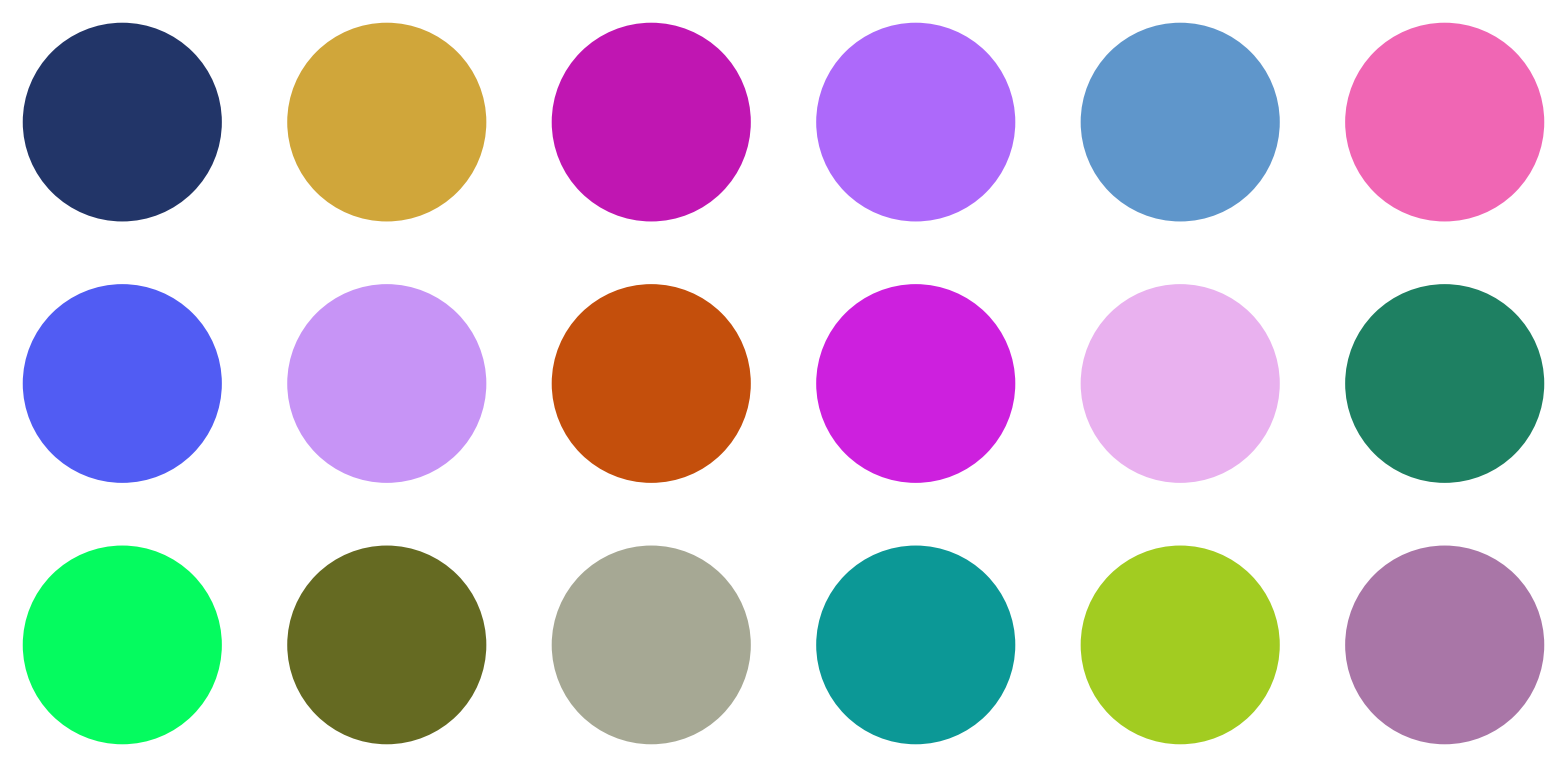

```mathematica
GraphicsGrid[Table[Graphics[Style[Disk[],RandomColor[]]],3,6]]
```

```mathematica
PieChart[EntityClass["Country","GroupOf5"][],ChartLabels->EntityList[EntityClass["Country","GroupOf5"]]]
```

-Graphics-

```mathematica
PieChart[EntityClass["Country","GroupOf5"][],ChartLegends->EntityList[EntityClass["Country","GroupOf5"]]]
```

-Graphics-

```mathematica
GraphicsGrid[Partition[PieChart[Counts[IntegerDigits[#]]]&/@Table[2^n,{n,25}],5]]
```

-Graphics-

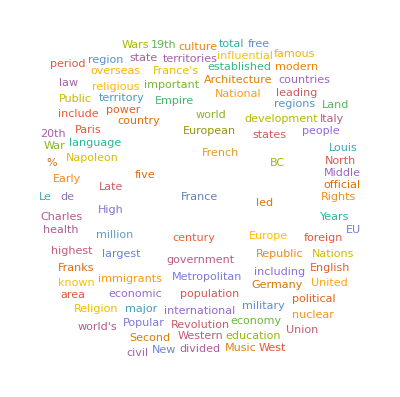
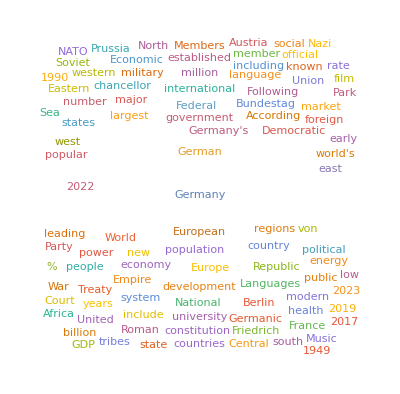
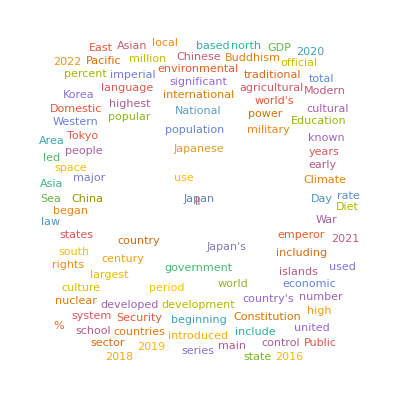
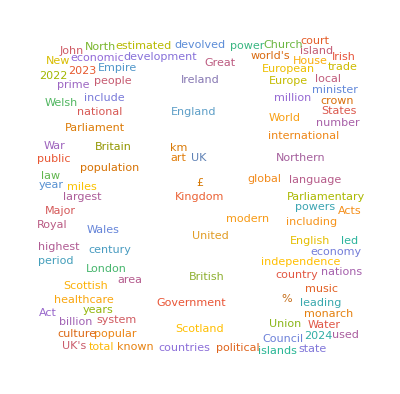
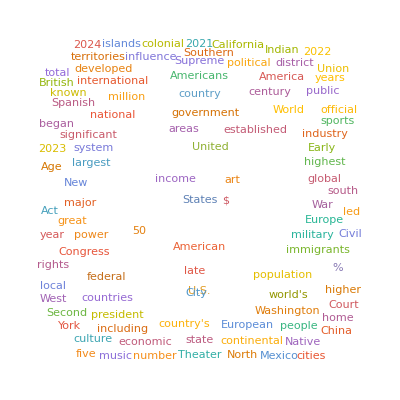

```mathematica
WordCloud[WikipediaData[#]]&/@EntityList[EntityClass["Country","GroupOf5"]]
```

# Chapter 38

```mathematica
Module[{x=Range[10]},x^2+x]
```

{2,6,12,20,30,42,56,72,90,110}

```mathematica
Module[{x=Table[RandomInteger[100],10]},Column[{x,Sort[x],Max[x],Total[x]}]]
```

{16,61,22,55,51,25,27,11,59,56}
{11,16,22,25,27,51,55,56,59,61}
61
383

```mathematica
Module[{x=Entity["TaxonomicSpecies","GiraffaCamelopardalis::y5488"][EntityProperty["TaxonomicSpecies","Image"]]},ImageCollage[{x,Blur[x],EdgeDetect[x],ColorNegate[x]}]]
```

-Graphics-

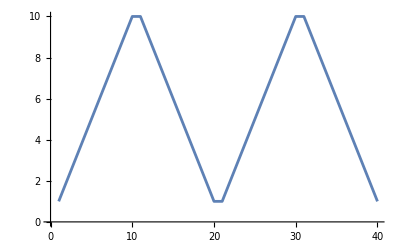

```mathematica
Module[{r=Range[10]},ListLinePlot[Join[r,Reverse[r],r,Reverse[r]]]]
```

```mathematica
Module[{x=Range[10]},{x+1,x-1,Reverse[x]}]
```

{{2,3,4,5,6,7,8,9,10,11},{0,1,2,3,4,5,6,7,8,9},{10,9,8,7,6,5,4,3,2,1}}

```mathematica
NestList[Mod[17#+2,11]&,10,20]
```

{10,7,0,2,3,9,1,8,6,5,10,7,0,2,3,9,1,8,6,5,10}

```mathematica
Table[StringJoin[
Module[{x,y},
x=Characters["aeiou"];
y=Complement[Alphabet[],x];
RandomChoice/@{x,y,x,y,x}]],10]
```

{ihuko,efeyi,ejoko,onibu,usoho,ugihu,ogixu,azawo,oyeta,upuxe}